Causality Constraints on Massive Gravity (1610.02033)

X.O. Camanho, G.L. Gómez, R. Rahman, 
Causality Constraints on Massive Gravity
https://arxiv.org/abs/1610.02033

#### Definitions

The Minkowski null frame and its inverse:

```mathematica
η=({{0, -1, 0}, {-1, 0, 0}, {0, 0, 1}});
iη=Inverse@η;  iη//MatrixForm
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | 1)

The inverse metric g:

```mathematica
g=({{F, -1/2, 0}, {-1/2, 0, 0}, {0, 0, 1}});
```

A vielbien of g:

```mathematica
Ε=({{-2^(-1/2) F, 2^(-1/2), 0}, {2^(-1/2), 0, 0}, {0, 0, 1}}); 
g==Transpose[Ε].η.Ε
```

True

The inverse metric g^-1:

```mathematica
ig=({{0, -2, 0}, {-2, -4 F, 0}, {0, 0, 1}}); 
ig==Inverse@g
```

True

A vielbien of g^-1:

```mathematica
itΕ=({{0, 2^(1/2), 0}, {2^(1/2), 2^(1/2)F, 0}, {0, 0, 1}});  
ig==Transpose[itΕ].iη.itΕ ∧itΕ==Inverse@Transpose@Ε
```

True

The particular field F for the sandwich pp-wave solution:

```mathematica
Fg[u_,r_,a_,λ_,m_]:=A[u,a,λ]BesselK[0,m r]
```

-Graphics-

```mathematica
A[u_,a_,λ_]:=Piecewise[{{a Exp[-(λ^2 u^2)/((u^2-λ^2)^2)], -λ<u<λ}, {0, True}}]
```

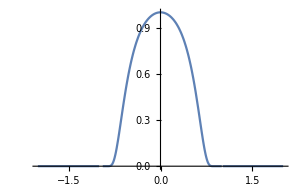
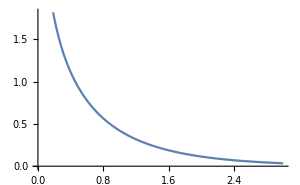

```mathematica
Row@{Plot[A[u,1,1],{u,-2,2},ImageSize->300],Plot[BesselK[0,r],{r,0,3},ImageSize->300]}
```

The null cone of g:

```mathematica
nc$g=({{𝕋u,𝕋v,𝕋r}}.g.Transpose[{{𝕋u,𝕋v,𝕋r}}])⟦1,1⟧//Simplify
```

𝕋r^2+𝕋u (F 𝕋u-𝕋v)

```mathematica
nc$3D[u_,v_,r_,a_,λ_,m_,scale1_:1,scale2_:1,options___]:=
Block[
{tvec$g,F},
F=Fg[N@u,N@r,a ,λ,m];
tvec$g=Normalize[ Normalize@itΕ⟦1⟧ + Normalize@itΕ⟦2⟧ ];
Translate[GeometricTransformation[Scale[
Join[
Normal@ContourPlot3D[
nc$g,
{𝕋v,-1,1},
{𝕋r,-1,1},
{𝕋u,-1,1},
options,
PlotRange->{{-3,3},{-3,3},{-3,3}},
Contours->{0},ContourStyle->{Opacity[0.2],Specularity[1,20]},
Mesh->None,Boxed->False,Axes->False,
Lighting->{{"Directional",LightYellow,{0.5,0.5,-5}}},
RegionFunction->Function [ {vv,rr,uu}, Abs[ {uu,vv,rr}.tvec$g ] ≤0.7]
]⟦1⟧,
{
Blue,Arrow@{{0,0,0},Normalize@itΕ⟦1,{2,3,1}⟧},
Red,Arrow@{{0,0,0},Normalize@itΕ⟦2,{2,3,1}⟧}
}
],scale1
],RotationMatrix[-45Degree,{0,1,0}]],{v,r,u}*scale2]
]
```

```mathematica
If[False,plot=Table[
nc$3D[u,0,r,0.93,1,1,0.07],
{u,Range[-1.2,1.2,0.2]},
{r,Range[0.2,1.2,0.2]}
];
Graphics3D[plot,Axes->True,AxesLabel->{"r","v","u"},PlotRange->All,ViewPoint->{-8,-3,0},ImageSize->500]
]
```

#### Null cone field and null geodesics

```mathematica
ncEllipsed[loc_,lVec_,nVec_,bθ_,scale_]:=
With[
{
a = Norm[ Normalize@lVec -Normalize@ nVec ],
c = Norm[ Normalize@lVec + Normalize@nVec ],
b = Sin[bθ] Norm[ Normalize@lVec + Normalize@nVec ] scale
},
With[
{p1 = (a √(c^2-b^2))/c,p2 = (c^2-b^2)/c},
	Translate[Rotate[
Scale[
	  {
		Line[{{-p1,p2},{0,0},{p1,p2}}],
		Line[{{-p1,-p2},{0,0},{p1,-p2}}],
		Thick, Circle[{0,c},{a,b}],
		Circle[{0,-c},{a,b},MinMax@{π-bθ/2,2π+bθ/2}],
		Thin,Dashed,Circle[{0,-c},{a,b},MinMax@{bθ/2,π-bθ/2}]
	  },
	scale ],
	  {{0,1},(Normalize@lVec + Normalize@nVec )/2}
],loc]
]]
```

```mathematica
Manipulate[
Block[{F,lVec,nVec},
F=Fg[N@u,N@r,N@a,N@λ,N@m];
lVec={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@ itΕ⟦1,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧};
nVec={#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@ itΕ⟦2,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧};
Row@{
Show[
StreamPlot[
{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@(itΕ⟦1,{1,2}⟧/.{u->t-z,v->t+z}),
{z,-3,3},
{t,-3,3},
StreamStyle->{Opacity[0.5],Blue,"Line"},
StreamPoints->{Table[{(-u+0)/2,(u+0)/2},{u,-3,3,0.5}],0.1,10},
ImageSize->{400,400}
],
StreamPlot[
{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@(itΕ⟦2,{1,2}⟧/.{u->t-z,v->t+z}),
{z,-3,3},
{t,-3,3},
StreamStyle->{Opacity[0.5],Red,"Line"},
StreamPoints->{Table[{(-0+v)/2,(0+v)/2},{v,-3,3,0.5}],0.1,10}
],
Graphics[{
Arrow[{zt,zt+0.6{1,1}}],Text[Style[v,15],zt+0.7{0.9,0.7}],
Arrow[{zt,zt+0.6{-1,1}}],Text[Style[u,15],zt+0.7{-0.9,0.7}],
ncEllipsed[zt,
{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@ itΕ⟦1,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧},
{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@ itΕ⟦2,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧},
0.3,0.25],
Blue,
Arrow[{zt,zt+0.3Normalize[{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@ (itΕ⟦1,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧})]}],
Red,
Arrow[{zt,zt+0.3Normalize[{#⟦2⟧-#⟦1⟧,#⟦1⟧+#⟦2⟧}/2&@( itΕ⟦2,{1,2}⟧/.{u->zt⟦2⟧-zt⟦1⟧,v->zt⟦2⟧+zt⟦1⟧})]}]
}],
Frame->True,
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
BaseStyle->{FontFamily->"Cambria",12},
FrameLabel->{Style[Row@{z," ⟶"},15,Darker@Green],Style[Row@{t,"  ⟶"},15,Darker@Green]}
],
Spacer[20],
If[in3D,
Graphics3D[
nc$3D[zt⟦2⟧-zt⟦1⟧,zt⟦2⟧+zt⟦1⟧,r,a,λ,m,1,1,PlotPoints->ControlActive[10,50]],
Boxed->False,Axes->{True,False,True},
AxesLabel->{Row@{z,"  ⟶"},None,Rotate[Row@{t,"  ⟶"},90Degree]},Ticks->None,PlotRange->All,
BaseStyle->{FontFamily->"Cambria",Bold,15},
ImageSize->{400,400},ViewPoint->Front
],
Graphics[{
Gray,
Arrow[0.6{{-1,-1},{1,1}}],Text[Style[v,15],0.7{0.9,0.7}],
Arrow[0.6{{1,-1},{-1,1}}],Text[Style[u,15],0.7{-0.9,0.7}],
Black,
Arrow[0.9{{0,-1},{0,1}}],Text[Style[t,15],{-0.1,0.8}],
Arrow[0.9{{-1,0},{1,0}}],Text[Style[z,15],{0.8,-0.1}],
ncEllipsed[{0,0},
lVec,
nVec,
0.3,0.25],
Blue,
Arrow[{{0,0},0.3Normalize@lVec}],
Text[Style[ℓ,15],0.3RotationMatrix[-10Degree].Normalize@lVec],
Red,
Arrow[{{0,0},0.3Normalize@nVec}],
Text[Style[𝓃,15],0.3RotationMatrix[10Degree].Normalize@nVec]
},
PlotRange->1,
BaseStyle->{FontFamily->"Cambria",12},
ImageSize->400
]
]
}
],
Control[{{r,0.1},0.01,3}],
Control[{{a,0.93},-1.5,1.5}],
Control[{{λ,1},0.1,1.5}],
Control[{{m,1},0.5,1.5}],
Control[{{zt,{0,0}},Locator}],
Control[{{in3D,False},{True,False}}],
SaveDefinitions->True,Deployed->True,AppearanceElements->None
]
```

#### Scattering on pp-waves

```mathematica
ticks[min_,max_]:=Join[Table[{i,Style[i,12],{.01,0}},{i,Ceiling[min],Floor[max]}],Table[{j+.5,,{.005,0}},{j,Round[min],Round[max-1],1}]]
```

```mathematica
particlePosition[t_,δ_,r$sep_,b$sep_]:=If[t≤-2.5,
{-δ-t,-r$sep/2+b$sep,0},
If[ t≤0.5,
{-δ+2.5,-r$sep/2+b$sep+(t+2.5),0},
If[t≤3,
{-δ+2.5+(t-0.5),r$sep/2-b$sep,0},
{-δ+5,r$sep/2-b$sep-(t-3),0}
]
]
]
```

```mathematica
particleTime[t_,δ_,r$sep_,b$sep_]:=t
```

```mathematica
With[
{r$sep=4,b$sep=1/2,δ=5},
Manipulate[
Row@{
Show[
Graphics3D[{
If[$ControlActiveSetting,Nothing,{
Arrowheads[{-0.024,0.024}],
Gray,Arrow@{{1,-r$sep/2,0},{1,r$sep/2,0}},
Black,Text[Style[r,15],{1,0,0.4}],
Gray,Arrow@{{0.5,-r$sep/2+b$sep,0},{0.5,r$sep/2-b$sep,0}},
Black,Text[Style[d,15],{0.5,0,0.4}],
Arrowheads[0.015],
Gray,Arrow@{{-1,-r$sep/2+b$sep+0.5,0},{-1,-r$sep/2+b$sep,0}},
Arrow@{{-1,-r$sep/2-0.5,0},{-1,-r$sep/2,0}},
Black,Text[Style[b,15],{-1,-r$sep/2+b$sep/2,0.1}]
}],
Arrowheads[0.024],
If[t<-2.5,Gray,LightGray],
Arrow@{{0,-r$sep/2+b$sep,0},{-δ+2.5,-r$sep/2+b$sep,0}},
If[-2.5≤t<0.5,Gray,LightGray],
Arrow@{{-δ+2.5,-r$sep/2+b$sep,0},{-δ+2.5,r$sep/2-b$sep,0}},
If[0.5≤t<3,Gray,LightGray],
Arrow@{{-δ+2.5,r$sep/2-b$sep,0},{0,r$sep/2-b$sep,0}},
If[3<t,Gray,LightGray],
Arrow@{{0,r$sep/2-b$sep,0},{0,-r$sep/2+b$sep,0}},
Arrowheads[0.024],Opacity[0.35],Specularity[1,20],
Blue,Arrow@Tube@{{-δ,-r$sep/2,0},{δ,-r$sep/2,0}},
Red,Arrow@Tube@{{δ,r$sep/2,0},{-δ,r$sep/2,0}},
(* Particle *)
Opacity[0.5],Specularity[1,20],Gray,
Sphere[particlePosition[t,δ,r$sep,b$sep],0.2],
Sphere[{particlePosition[t,δ,r$sep,b$sep]⟦1⟧,δ-0.1,0.2},0.1]
},
PlotRange->{{-δ,δ},{-δ,δ},{-δ,δ}/2},
Boxed->True,Axes->True,AxesLabel->(Style[#,15]&/@{z,x,y}),
FaceGrids->{{{-1,0,0},{Range[-δ,δ,0.5],Range[-δ,δ,0.5]}}},
FaceGridsStyle->Directive[Dashed,LightGray],
BaseStyle->{FontFamily->"Cambria",FontSize->14},
Ticks->{ticks[-δ,δ],ticks[-δ,δ],ticks[-δ,δ]},
ImageSize->600
],
SliceDensityPlot3D[   (* F[u], moving along v *)
Abs@Fg[(*u*) t-z+2,((x+r$sep/2)^2+y^2)^(1/2),a,λ,m],
ControlActive[{t-z+2==0},{Thread[t-z+2==Subdivide[-2/3λ,2/3λ,6]]}],
{z,-δ,δ},
{x,-δ,δ},
{y,-δ,δ},
PlotRange->{0.1,5},BoundaryStyle->None,
ColorFunction->(Directive[Blue,Opacity@Rescale[#,{0.1,1},{0.15,0.9}]]&)
],
SliceDensityPlot3D[  (* F[v], moving along u *)
Abs@Fg[(*v*) t+z,((x-r$sep/2)^2+y^2)^(1/2),a,λ,m],
ControlActive[{t+z==0},{Thread[t+z==Subdivide[-2/3λ,2/3λ,6]]}],
{z,-δ,δ},
{x,-δ,δ},
{y,-δ,δ},
PlotRange->{0.1,5},BoundaryStyle->None,
ColorFunction->(Directive[Red,Opacity@Rescale[#,{0.1,1},{0.15,0.9}]]&)
],
ParametricPlot3D[
{
{z,δ,A[t-z+2,a,λ]}, (* u *)
{z,δ-0.1,A[t+z,a,λ]} (* v *)
},
{z,-δ,δ},
PlotStyle->{{Opacity[0.5],Blue},{Opacity[0.5],Red}}
]
],
Spacer[20],
ParametricPlot[
{
{z,t+A[t-z,a,λ]}, (* u *)
{z,t+A[t+z,a,λ]} (* v *)
},
{z,-δ,δ},
Epilog->{PointSize[0.02],Point[{
particlePosition[t,δ,r$sep,b$sep]⟦1⟧,particleTime[t,δ,r$sep,b$sep]
}]
},
PlotRange->{{-δ,δ},{-δ,δ+1}},
PlotStyle->{{Opacity[0.5],Blue},{Opacity[0.5],Red}},
BaseStyle->{FontFamily->"Cambria",12},
FrameLabel->{Style[Row@{z," ⟶"},15,Darker@Green],Style[Row@{time,"  ⟶"},15,Darker@Green]},
Frame->True,AspectRatio->1,
ImageSize->400
]
},
Panel@Row[{
Column@{
Control[{{a,0.93},-1.5,1.5}],
Control[{{λ,1},0.1,1.5}],
Control[{{m,1},0.5,1.5}]
},
Spacer[20],
Column@{
Control[{{t,-δ},-δ,δ+1,0.1,AnimationRate->1/5,Appearance->"Open"}]
}
}],
SaveDefinitions->True,AppearanceElements->None,Paneled->False
]
]
```

```mathematica
particleTime2[t_,δ_,r$sep_,b$sep_]:=If[t≤-3,t,
If[ t≤-2.5,-3-(t+3),
If[t≤1,-4+(t+2.5),
If[t≤2,
0-(t-1),
0+(t-2)
]
]
]
]
```

## todo...

```mathematica
MatrixForm@({{a, b, 0}, {b, c, 0}, {0, 0, 1}})/.Solve[Thread[Flatten[({{F, -1/2, 0}, {-1/2, G, 0}, {0, 0, 1}})-Transpose[({{a, b, 0}, {2^(-1/2), c, 0}, {0, 0, 1}})].η.({{a, b, 0}, {2^(-1/2), c, 0}, {0, 0, 1}})]==0]//Union,{a,c,b}]//Simplify;
```

```mathematica
ΕFG[F_,G_]:=Piecewise[{{({{0, 2^(-1/2), 0}, {2^(-1/2), 0, 0}, {0, 0, 1}}), F==0∧G==0}, {({{-F/(√2), (1+√(1-4 F G))/(2 √2), 0}, {(1+√(1-4 F G))/(2 √2), (-1+√(1-4 F G))/(2 √2 F), 0}, {0, 0, 1}}), G==0}, {({{(-1+√(1-4 F G))/(2 √2 G), (1+√(1-4 F G))/(2 √2), 0}, {(1+√(1-4 F G))/(2 √2), -G/(√2), 0}, {0, 0, 1}}), True}}]
```

## GUI

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-